## Week 2 – Stanford Machine Learning

### Multivariate Regression

Let us create some random data, say housing size, number of bedrooms, and age of the house as a feature matrix, and price levels on y. Although we deal with a multi-dimensional case, traditionally we consider the training features as a part of x and the training labels as a part of y.

```mathematica
trainX={{100,320,213,512,58,84,113}, {1,4,2,4,0,1,1},{7,4,12,21,9,3,31}};
trainY={140000,400000,241000,489000,78000,123000,139000};
grid=Grid[MapThread[Prepend,{Prepend[Transpose@Append[trainX,trainY],{"Size (feet^2)","Bedrooms","Age (years)","Price ($)"}],Join[{"Examples"},Range[1,7]]}],Dividers->Center]
```

Examples | Size (feet^2) | Bedrooms | Age (years) | Price ($)
1 | 100 | 1 | 7 | 140000
2 | 320 | 4 | 4 | 400000
3 | 213 | 2 | 12 | 241000
4 | 512 | 4 | 21 | 489000
5 | 58 | 0 | 9 | 78000
6 | 84 | 1 | 3 | 123000
7 | 113 | 1 | 31 | 139000

Now, we define a our hypothesis function which is the dot product between any two n-dimensional vectors

```mathematica
Hyp[v_,x_]:=Dot[v,x]
```

```mathematica
Transpose@{1,2,3}
```

Transpose::nmtx: The first two levels of {1, 2, 3} cannot be transposed.

Transpose[{1,2,3}]

followed by the squared error cost function

```mathematica
Cost[v1_,v2_]:=1/(2Length[trainX])Total[(Hyp[{v1,v2},#1]-#2)^2&@@@Transpose@{trainX,trainY}];
```

We then minimise the cost function, after which we plot the hypothesis function with the minimised values

{3.49273×10^8,{v1→43289.8,v2→933.551}}

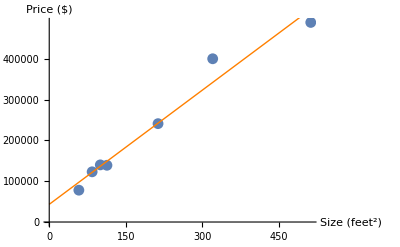

```mathematica
regression=Minimize[Cost[v1,v2],{v1,v2}]//N
regpp:=Plot[Hyp[{v1,v2}/.regression[[2]],x],{x,0,Max[trainX]},PlotStyle->{Orange,Thin}];
Show[reglp,regpp]
```

### Gradient Descent

Let us repeat the regression analysis by using gradient descent instead. First, we take the same data, and plot it

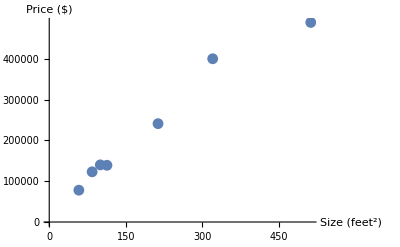

```mathematica
trainX={100,320,213,512,58,84,113};
trainY={140000,400000,241000,489000,78000,123000,139000};
gdlp=ListPlot[Transpose@{trainX,trainY},AxesLabel->{"Size (feet^2)","Price ($)"}];
Show[gdlp]
```

We define the same hypothesis and cost functions

```mathematica
Hyp[v_,x_]:=v[[1]]+v[[2]] x;
Cost[v1_,v2_]:=1/(2Length[trainX])Total[(Hyp[{v1,v2},#1]-#2)^2&@@@Transpose@{trainX,trainY}];
```

And then we create the step function that returns the next step of the gradient descent algorithm. We also assign the learning rates. Note that because of the huge values on the pricing axis, the y values are particularly sensitive to the learning rate parameter. Any learning rate above 1 10^-5 will thus make the gradient descent algorithm overshoot. Instead of setting a very low learning rate parameter, as below, a better fix would be to represent the housing prices in terms of thousand dollars.

```mathematica
αv1=0.1;
αv2 =0.00001;
Step[v1_,v2_]:=
{v1-αv1 D[Cost[x,y],x]/.{x->v1,y->v2},v2-αv2 D[Cost[x,y],y]/.{x->v1,y->v2}};
```

To check that the step function works, we can plot the step function as a function of the iteration number to picture the learning rate. We do so by creating the learning function

```mathematica
Learning[x_]:=Cost@@Nest[Apply[Step,#]&,{1,1},x];
```

We do indeed learn, as seen in the plot below

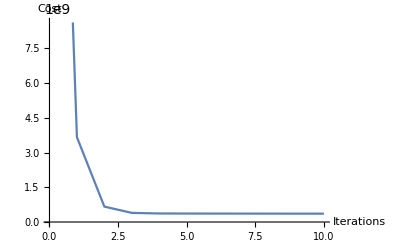

```mathematica
learningRate=ListLinePlot[#,AxesLabel->{"Iterations","Cost"}]&@Transpose@{Range[0,10],Learning/@Range[0,10]}
```

We then step through the algorithm ten times and plot all the lines of all intermediate steps to see how the regression converges towards the optimum

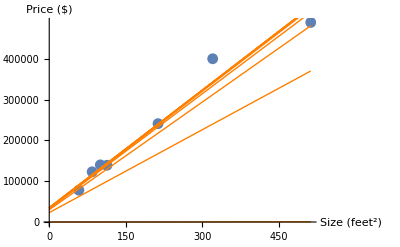

```mathematica
gd=NestList[Apply[Step,#]&,{1,1},10];
gdpp=Show[Plot[Hyp[#1,x],{x,0,Max[trainX]},PlotStyle->{Orange,Thin}]&/@gd];
Show[gdlp,gdpp]
```